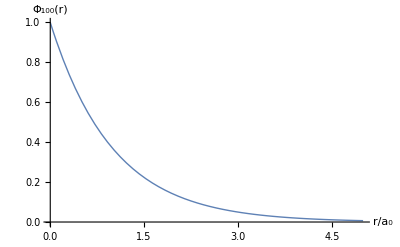

```mathematica
p = Plot[Exp[-x], {x,0,5}, AxesLabel->{"r/a_0" // fs, "Φ_100(r)" // fs}, Ticks -> None, PlotStyle->Thick]

fs = Style[#, FontSize-> 16]&;
```

```mathematica
<<peeters` ;
peeters`setGitDir[ "../project/figures/phy456-qmII" ]
```

/Users/pjoot/project/figures/phy456-qmII

```mathematica
peeters`exportForLatex["hydrogenGroundStateFig2", p]
```

{hydrogenGroundStateFig2.eps,hydrogenGroundStateFig2pn.png}

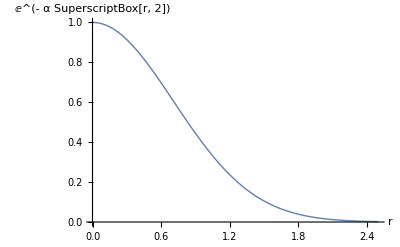

```mathematica
p2 = Plot[Exp[-x^2], {x,0,2.5}, AxesLabel->{"r" // fs, "ⅇ^(- α SuperscriptBox[r, 2])" // fs}, Ticks -> None, PlotStyle->Thick]
```

```mathematica
peeters`exportForLatex["hydrogenGroundStateFig4", p2]
```

{hydrogenGroundStateFig4.eps,hydrogenGroundStateFig4pn.png}

```mathematica
Manipulate[ Plot[ 
{Callout[x - a Sqrt[x], "α_0" // fs, Below],
x - a Sqrt[x]}, {x,0,2}, Ticks -> None, PlotStyle-> Thick,
AxesLabel->{"α" // fs, "E(α)" // fs}
],
{{a,1.2},0,2}]
```

```mathematica
p3 = DynamicModule[{a=1.2},Plot[{Callout[x-a √x,fs["\!\(\*SubscriptBox[\(α\), \(0\)]\)"],Below],x-a √x},{x,0,2},Ticks->None,PlotStyle->Thick,AxesLabel->{fs["α"],fs["E(α)"]}]]
```

```mathematica
peeters`exportForLatex["hydrogenGroundStateFig5", p3]
```

{hydrogenGroundStateFig5.eps,hydrogenGroundStateFig5pn.png}